# TC Loading model

System of equations considering steady state of TC, aa-tRNA, and free uncharged tRNA

```mathematica
eqsystem={trnafree + aatrna + tc + rao == trnatotal,
rao + raf == rtotal,
kch*trnafree*atp - ktc*gtp*aatrna +ktcrev*tc== 0,
ktc*gtp*aatrna-kl*tc*raf -ktcrev*tc== 0,
ktr*rao*gtp - kch*trnafree*atp  == 0}
```

{aatrna+rao+tc+trnafree==trnatotal,raf+rao==rtotal,-aatrna gtp ktc+ktcrev tc+atp kch trnafree==0,aatrna gtp ktc-ktcrev tc-kl raf tc==0,gtp ktr rao-atp kch trnafree==0}

Solving

```mathematica
$Assumptions=_∈NonNegativeReals
```

_∈ℝ&&_≥0

```mathematica
solution = Solve[eqsystem,{tc,raf, rao, trnafree, aatrna}]
```

{{tc→1/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))(-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)),raf→rtotal-trnatotal+1/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))(-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2))+1/(atp kch ktc+atp kch ktr+gtp ktc ktr)(gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev)))+1/(gtp ktc)((ktcrev (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))+1/(atp kch ktc+atp kch ktr+gtp ktc ktr)atp kch (gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev)))),rao→trnatotal-1/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))(-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2))-1/(atp kch ktc+atp kch ktr+gtp ktc ktr)(gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev)))-1/(gtp ktc)((ktcrev (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))+1/(atp kch ktc+atp kch ktr+gtp ktc ktr)atp kch (gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev)))),trnafree→1/(atp kch ktc+atp kch ktr+gtp ktc ktr)(gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))),aatrna→1/(gtp ktc)((ktcrev (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))+1/(atp kch ktc+atp kch ktr+gtp ktc ktr)atp kch (gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))))},{tc→1/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))(-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)),raf→rtotal-trnatotal+1/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))(-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2))+1/(atp kch ktc+atp kch ktr+gtp ktc ktr)(gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev)))+1/(gtp ktc)((ktcrev (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))+1/(atp kch ktc+atp kch ktr+gtp ktc ktr)atp kch (gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev)))),rao→trnatotal-1/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))(-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2))-1/(atp kch ktc+atp kch ktr+gtp ktc ktr)(gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev)))-1/(gtp ktc)((ktcrev (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))+1/(atp kch ktc+atp kch ktr+gtp ktc ktr)atp kch (gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev)))),trnafree→1/(atp kch ktc+atp kch ktr+gtp ktc ktr)(gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))),aatrna→1/(gtp ktc)((ktcrev (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))+1/(atp kch ktc+atp kch ktr+gtp ktc ktr)atp kch (gtp ktc ktr trnatotal-(gtp ktc ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))-(ktcrev ktr (-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2)))/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))))}}

There are 2 solutions to the equation, we will examine which one to take and whether they make biological sense.

```mathematica
tcsolution1 = solution[[1]][[1]]
```

tc→1/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))(-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal-√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2))

```mathematica
tcsolution2 = solution[[2]][[1]]
```

tc→1/(2 (atp gtp kch kl ktc+atp kch kl ktcrev))(-atp gtp^2 kch ktc ktr-atp gtp kch ktcrev ktr-atp gtp kch kl ktc rtotal-atp gtp kch kl ktr rtotal-gtp^2 kl ktc ktr rtotal+atp gtp kch kl ktc trnatotal+√(4 atp gtp^2 kch ktc (atp gtp kch kl ktc+atp kch kl ktcrev) ktr trnatotal+(atp gtp^2 kch ktc ktr+atp gtp kch ktcrev ktr+atp gtp kch kl ktc rtotal+atp gtp kch kl ktr rtotal+gtp^2 kl ktc ktr rtotal-atp gtp kch kl ktc trnatotal)^2))

```mathematica
$Assumptions={atp>0, gtp>0,trnatotal>0,tc>0,raf>0, rtotal>0, rao>0,trnafree>0,aatrna>0, kl>0, ktr>0, kch>0, ktc>0, ribosomes>0, trnatotal>0, rtotal>0,ktcrev>0}
```

{atp>0,gtp>0,trnatotal>0,tc>0,raf>0,rtotal>0,rao>0,trnafree>0,aatrna>0,kl>0,ktr>0,kch>0,ktc>0,ribosomes>0,trnatotal>0,rtotal>0,ktcrev>0}

```mathematica
FullSimplify[tcsolution1]
```

tc→-1/(2 atp kch kl (gtp ktc+ktcrev))gtp (gtp kl ktc ktr rtotal+atp kch (gtp ktc ktr+ktcrev ktr+kl (ktc+ktr) rtotal-kl ktc trnatotal)+√(4 atp^2 kch^2 kl ktc (gtp ktc+ktcrev) ktr trnatotal+(gtp kl ktc ktr rtotal+atp kch (gtp ktc ktr+ktcrev ktr+kl (ktc+ktr) rtotal-kl ktc trnatotal))^2))

TC in steady state as a function of total number of tRNAs , ribosomes demanding or translating the corresponding codon, ATP and GTP:

```mathematica
ftcatpgtp1[atp_, gtp_, trnatotal_, rtotal_, ktc_, kl_, kch_, ktr_, ktcrev_]:=-1/(2 atp kch kl (gtp ktc+ktcrev))gtp (gtp kl ktc ktr rtotal+atp kch (gtp ktc ktr+ktcrev ktr+kl (ktc+ktr) rtotal-kl ktc trnatotal)+√(4 atp^2 kch^2 kl ktc (gtp ktc+ktcrev) ktr trnatotal+(gtp kl ktc ktr rtotal+atp kch (gtp ktc ktr+ktcrev ktr+kl (ktc+ktr) rtotal-kl ktc trnatotal))^2))
```

TC in steady state for ATP,GTP->infinity and ATP,GTP ->0

```mathematica
FullSimplify[ftcatpgtp1[atp, 0, trnatotal, rtotal, ktc, kl, kch, ktr, ktcrev]]
```

0

```mathematica
Limit[FullSimplify[ftcatpgtp1[atp, atp,trnatotal, ribosomes,  ktc, kl, kch, ktr, ktcrev]],atp-> 0 ]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

```mathematica
Limit[FullSimplify[ftcatpgtp1[atp, gtp,trnatotal, ribosomes,  ktc, kl, kch, ktr, ktcrev]],atp-> +∞ ]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-(gtp (kch (gtp ktc ktr+ktcrev ktr+kl (ktc+ktr) ribosomes-kl ktc trnatotal)+kch √(4 kl ktc (gtp ktc+ktcrev) ktr trnatotal+(gtp ktc ktr+ktcrev ktr+kl (ktc+ktr) ribosomes-kl ktc trnatotal)^2)))/(2 kch kl (gtp ktc+ktcrev))

```mathematica
Limit[FullSimplify[ftcatpgtp1[atp, atp,trnatotal, ribosomes,  ktc, kl, kch, ktr, ktcrev]],atp-> +∞ ]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-∞

Solution seems invalid because if atp and gtp -> infinity the concentration takes negative values.

TC in steady state as a function of ATP, assuming that GTP~0.1*ATP:

```mathematica
ftcatp1[atp_, trnatotal_,rtotal_, ktc_, kl_, kch_, ktr_, ktcrev_]:=ftcatpgtp1[atp,0.1*atp,trnatotal,rtotal, ktc, kl, kch, ktr, ktcrev]
```

Considering 5 last rate constant parameters, ATP concentration 3mM, tRNA concentration of 0.1uM and 0.01uM for the concentration of ribosomes demanding or translating the specific codon, the amount of ternary complexes is:

```mathematica
ftcatp1[3*10^-3,10^-7,10^-8, 10^5, 10^6, 10^1,10^6, 10^-2 ]
```

-0.000400052

Solution is invalid because concentration takes negative values.

```mathematica
FullSimplify[tcsolution2]
```

tc→1/(2 atp kch kl (gtp ktc+ktcrev))gtp (-gtp ktc ktr (atp kch+kl rtotal)-atp kch (ktcrev ktr+kl (ktc+ktr) rtotal-kl ktc trnatotal)+√(4 atp^2 kch^2 kl ktc (gtp ktc+ktcrev) ktr trnatotal+(gtp kl ktc ktr rtotal+atp kch (gtp ktc ktr+ktcrev ktr+kl (ktc+ktr) rtotal-kl ktc trnatotal))^2))

TC in steady state as a function of total number of tRNAs , ribosomes demanding or translating the corresponding codon, ATP and GTP:

```mathematica
ftcatpgtp2[atp_, gtp_, trnatotal_, rtotal_, ktc_, kl_, kch_, ktr_,  ktcrev_]:=1/(2 atp kch kl (gtp ktc+ktcrev))gtp (-gtp ktc ktr (atp kch+kl rtotal)-atp kch (ktcrev ktr+kl (ktc+ktr) rtotal-kl ktc trnatotal)+√(4 atp^2 kch^2 kl ktc (gtp ktc+ktcrev) ktr trnatotal+(gtp kl ktc ktr rtotal+atp kch (gtp ktc ktr+ktcrev ktr+kl (ktc+ktr) rtotal-kl ktc trnatotal))^2))
```

TC in steady state for ATP,GTP->infinity and ATP,GTP ->0

```mathematica
FullSimplify[ftcatpgtp2[atp, 0, trnatotal, rtotal, ktc, kl, kch, ktr, ktcrev]]
```

0

```mathematica
Limit[FullSimplify[ftcatpgtp2[atp, atp,trnatotal, ribosomes,  ktc, kl, kch, ktr,  ktcrev]],atp-> 0 ]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

```mathematica
Limit[FullSimplify[ftcatpgtp2[atp, gtp,trnatotal, ribosomes,  ktc, kl, kch, ktr,  ktcrev]],atp-> +∞ ]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/(2 kch kl (gtp ktc+ktcrev))gtp (-gtp kch ktc ktr-kch (ktcrev ktr+kl (ktc+ktr) ribosomes-kl ktc trnatotal)+kch √(4 kl ktc (gtp ktc+ktcrev) ktr trnatotal+(gtp ktc ktr+ktcrev ktr+kl (ktc+ktr) ribosomes-kl ktc trnatotal)^2))

```mathematica
Limit[FullSimplify[ftcatpgtp2[atp, atp,trnatotal, ribosomes,  ktc, kl, kch, ktr, ktcrev]],atp-> +∞ ]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

trnatotal

As atp and gtp -> infinity the concentration only depends on the number of tRNAs

TC in steady state as a function of ATP, assuming that GTP~0.1*ATP:

```mathematica
ftcatp[atp_, trnatotal_,rtotal_, ktc_, kl_, kch_, ktr_,ktcrev_]:=ftcatpgtp2[atp,0.1*atp,trnatotal,rtotal, ktc, kl, kch, ktr, ktcrev]
```

Considering 5 last rate constant parameters, ATP concentration 3mM, tRNA concentration of 0.1uM and 0.01uM for the concentration of ribosomes demanding or translating the specific codon, the amount of ternary complexes is:

```mathematica
ftcatp[3*10^-3,10^-7,10^-7, 10^5, 10^7, 10^3,10^6, 10^-2 ]
```

7.30228×10^-8

For 0.1uM of tRNAs ~ 0.073uM can be found in ternary complex (for 0.1uM of ribosomes translating the codon)

```mathematica
ftcatpexparameters[atp_, trnatotal_,rtotal_]:=ftcatp[atp,trnatotal,rtotal,10^5, 10^7, 10^3,10^6,10^-2 ]
```

```mathematica
atpmax = 0.01;
Manipulate[Overlay[{Plot[x*ftcatpexparameters[atpmax, trnalevels, rtotal]/atpmax , {x, 0, atpmax}, PlotStyle->Dashed,AxesLabel-> {"ATP [M]", "TC [M]"}, PlotRange->{{0, atpmax},{0,trnalevels}}], Plot[ftcatpexparameters[atp, trnalevels, rtotal], {atp, 0, atpmax},PlotRange->{{0, atpmax},{0,trnalevels}}, AxesLabel-> {"ATP [M]", "TC [M]"}]}], {{trnalevels, 1*10^-7}, 0 , 1*10^-6}, {{rtotal, 1*10^-7}, 0 , 1*10^-7}]
```

Plot::plln: Limiting value atpmax in {x,0,atpmax} is not a machine-sized real number.

Plot::plln: Limiting value atpmax in {atp,0,atpmax} is not a machine-sized real number.

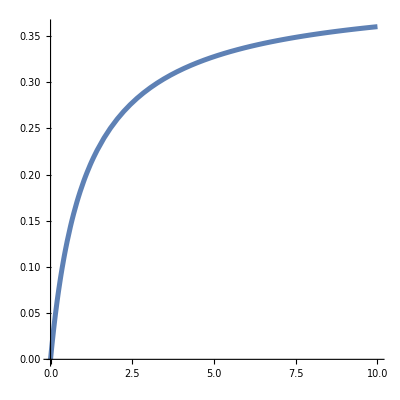
-Graphics-Ternary complex [μM]ATP [mM]

```mathematica
Labeled[Plot[10^6*ftcatpexparameters[atp/1000, 4*10^-7, 10^-7] ,{atp,0, 10},  AspectRatio->1/1, PlotStyle->{Thickness[.009]}, TicksStyle->Directive[FontSize->18]],{"Ternary complex [μM]", "ATP [mM]"},  {Left, Bottom},LabelStyle->{FontSize->20,FontFamily->"Arial"},RotateLabel->True]
```

Ratio of TCs for different codons 1 and 2 in steady state, as a function of atp, trnas 1 and 2 and ribosomes for 1 and 2:

```mathematica
fratioatp[atp_, trnalevel1_, trnalevel2_, rtotal1_, rtotal2_,  ktc_, kl_, kch_, ktr_, ktcrev_] := ftcatp[atp, trnalevel1, rtotal1, ktc, kl, kch, ktr,ktcrev]/ftcatp[atp,trnalevel2, rtotal2,ktc, kl, kch, ktr,ktcrev]
```

```mathematica
FullSimplify[fratioatp[atp,trnalevel1, trnalevel2, rtotal1, rtotal2, ktc, kl, kch, ktr,ktcrev]]
```

(1. (-0.1 atp ktc ktr (atp kch+kl rtotal1)-atp kch (ktcrev ktr+kl (ktc+ktr) rtotal1-kl ktc trnalevel1)+√(4 atp^2 kch^2 kl ktc (0.1 atp ktc+ktcrev) ktr trnalevel1+(0.1 atp kl ktc ktr rtotal1+atp kch (0.1 atp ktc ktr+ktcrev ktr+kl (ktc+ktr) rtotal1-kl ktc trnalevel1))^2)))/(-0.1 atp ktc ktr (atp kch+kl rtotal2)-atp kch (ktcrev ktr+kl (ktc+ktr) rtotal2-kl ktc trnalevel2)+√(4 atp^2 kch^2 kl ktc (0.1 atp ktc+ktcrev) ktr trnalevel2+(0.1 atp kl ktc ktr rtotal2+atp kch (0.1 atp ktc ktr+ktcrev ktr+kl (ktc+ktr) rtotal2-kl ktc trnalevel2))^2))

```mathematica
fratioatpexparameters[atp_, trnalevel1_, trnalevel2_, rtotal1_, rtotal2_]:=fratioatp[atp,trnalevel1, trnalevel2, rtotal1, rtotal2,10^5, 10^7, 10^3,10^6,10^-2 ]
```

```mathematica
SetOptions[Plot,BaseStyle->FontSize->16];
```

```mathematica
atpmax=0.01;
Manipulate[Plot[fratioatpexparameters[atp, trnalevel1, trnalevel2, rtotal1, rtotal2] ,{atp,0, atpmax}, AxesLabel->{"ATP [M]","Loading speed codon 1/codon2" }],{{trnalevel1, 4*10^-7},0,10^-6},{{trnalevel2, 2*10^-7},0,10^-6}, {{rtotal1, 1*10^-7},0,10^-6}, {{rtotal2, 8*10^-7},0,10^-6}]
```

Plot::plln: Limiting value atpmax in {atp,0,atpmax} is not a machine-sized real number.

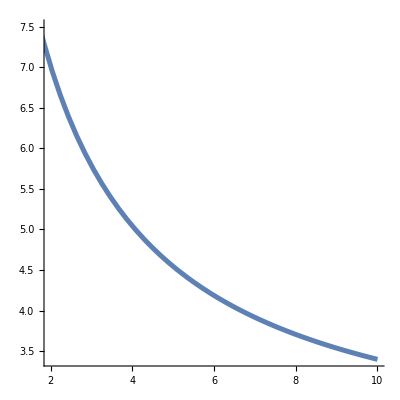
-Graphics-Fast-to-slow TC loading rate ratioATP [mM]

```mathematica
p=Labeled[Plot[fratioatpexparameters[atp/1000, 4*10^-7,  2*10^-7, 1*10^-7, 8*10^-7] ,{atp,0, 10},  AspectRatio->1/1, PlotStyle->{Thickness[.009]}, PlotRange-> {{2,10}, {Automatic, 7.5}}, TicksStyle->Directive[FontSize->18]],{"Fast-to-slow TC loading rate ratio", "ATP [mM]"},  {Left, Bottom},LabelStyle->{FontSize->20,FontFamily->"Arial"},RotateLabel->True]
```

```mathematica
Export["fast_slow_ratio_atp.png",p]
```

fast_slow_ratio_atp.png

```mathematica
trnalevel1=4*10^-7;
trnalevel2 = 2*10^-7;
rtotal1 = 1*10^-7;
rtotal2 = 8*10^-7;
atpboundmin=2*10^-3;
atpboundmax=6*10^-3;
```

```mathematica
ratiomaxmin = fratioatpexparameters[atpboundmax, trnalevel1, trnalevel2, rtotal1, rtotal2]/fratioatpexparameters[atpboundmin, trnalevel1, trnalevel2, rtotal1, rtotal2]
```

0.596534

Calculate change in TC loading ratio across multiple kinetic rates

```mathematica
fratiodecfcpercentage[atpboundmax_, atpboundmin_, trnalevel1_, trnalevel2_, rtotal1_, rtotal2_,  ktc_, kl_, kch_, ktr_, ktcrev_]:=-100*(1- fratioatp[atpboundmax,trnalevel1, trnalevel2, rtotal1, rtotal2,ktc, kl, kch, ktr,  ktcrev]/fratioatp[atpboundmin,trnalevel1, trnalevel2, rtotal1, rtotal2,ktc, kl, kch, ktr, ktcrev])
```

```mathematica
fratiodecfcpercentage[atpboundmax, atpboundmin, trnalevel1, trnalevel2, rtotal1, rtotal2,10^5, 10^7, 10^3,10^6,10^-2 ]
```

-40.3466

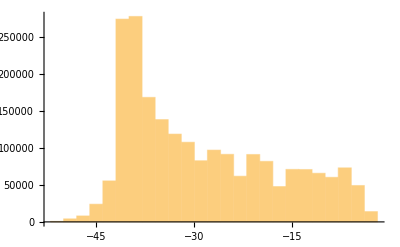

```mathematica
step=.1;
fclist = Flatten[Table[fratiodecfcpercentage[atpboundmax, atpboundmin, trnalevel1, trnalevel2, rtotal1, rtotal2,10^logktc, 10^logkl, 10^logkch,10^logktr, 10^logktcrev], {logktc,4,6,step}, {logkl,7,8,step}, {logkch, 2, 4,step}, {logktr,5,7,step},{logktcrev,-3,-1,step}]];
Histogram[fclist]
```

```mathematica
SetOptions[Plot,BaseStyle->{14,Directive[FontFamily->"Arial"]}];
```

```mathematica
SetOptions[Graphics,BaseStyle->{FontFamily->"Arial"}]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{FontFamily→Arial},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

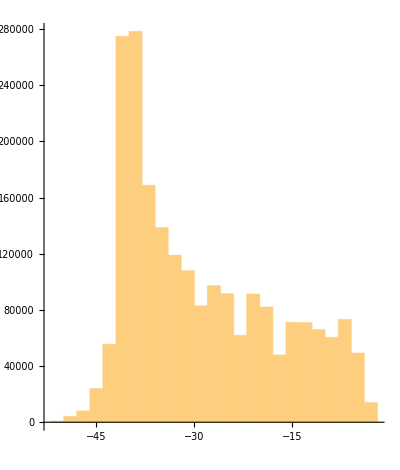
-Graphics-Number of 
simulationsLoading ratio decrease

```mathematica
p = Labeled[Histogram[fclist,LabelStyle->{FontSize->14}, AspectRatio->2/1.7],{"Number of \nsimulations", "Loading ratio decrease"},  {Left, Bottom},LabelStyle->{FontSize->16,FontFamily->"Arial"},RotateLabel->True]
```

```mathematica
yticks={#*10^3,ToString[#]<>"k"}&/@(Range[10]*50);
```

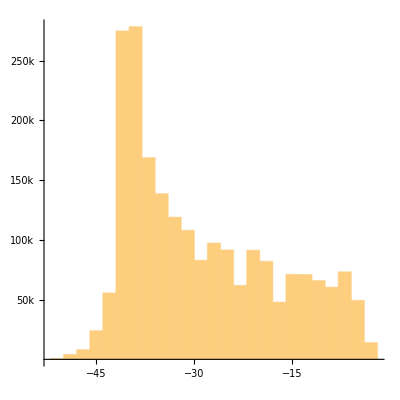
-Graphics-Simulations   Loading ratio decrease

```mathematica
p = Labeled[Histogram[fclist,LabelStyle->{FontSize->14}, AspectRatio->1/1, Ticks->{Automatic,yticks}],{"Simulations", "   Loading ratio decrease"},  {Left, Bottom},LabelStyle->{FontSize->16,FontFamily->"Arial"},RotateLabel->True]
```

```mathematica
Export["loading_ratio_n_histogram.pdf",p]
```

loading_ratio_n_histogram.pdf